## Neuman wS Active

### Технические вещи

```mathematica
Needs["NDSolve`FEM`"]
Mon [prog_]:=
Monitor[
Timing[
ReleaseHold[prog];
][[1]],
{
step," / ",tmax," ",
ProgressIndicator[step,{0,tmax}]
}//Row
];
```

### Основные константы:

```mathematica
({{xmin, xmax}}):=({{-1, 10}});
tmax:=100;
rate:={
V->γ If [2<x<3&& m[t,x]>=0.0001,0.7m[t,x](-Log[m[t,x]/(1-n[t,x])])^((γ-1.)/γ),0]};
γ:=4;
({{in}, {ip}}):=({{0.1}, {0.001}});
```

### Тензоры диффузионных потоков

```mathematica
dNM:={{0.1}};
dMP:={{0.01}};
dPN:={{0.01}};
```

### Уравнения

```mathematica
(*
Основная система
*)
eq:=Inactivate[
{
D[n[t,x], {t}]+jN{x}==Γn,
D[p[t,x], {t}]+jP{x}-V==Γp
},
Div|D|Grad];

(*
Потоки
*)
fluxes:=Inactivate[
{
jN->-(m[t,x] dNM).n[t,x]{x}-(p[t,x] dPN).n[t,x]{x}+(n[t,x] dNM).m[t,x]{x}+(n[t,x] dPN).p[t,x]{x},
jP->-(m[t,x] dMP).p[t,x]{x}-(n[t,x] dPN).p[t,x]{x}+(p[t,x] dMP).m[t,x]{x}+(p[t,x] dPN).n[t,x]{x}
},
Div|D|Grad];

(*
Граничные потоки
*)
bound:=
{
Γn->NeumannValue[0,x==xmin || x==xmax],
Γp->NeumannValue[0,x==xmin || x==xmax]
}
(*
Начальные и граничные условия
*)
ibcs:=
{
n[0,x]==in,
p[0,x]==ip(*,
DirichletCondition[n[t,x]==in,True],
DirichletCondition[p[t,x]==ip,True]*)
};

rep={m[t,x]->1-n[t,x]-p[t,x]};
```

```mathematica
solve:= NDSolve[
solPDE,
{n,p},
{t,0.,tmax},
{x,xmin,xmax},
EvaluationMonitor :> Sow[step = t],
Method->{
"PDEDiscretization"->{
"MethodOfLines",
"SpatialDiscretization"->
{
"FiniteElement",
"MeshOptions"->{"MaxCellMeasure"->0.1,"MeshOrder"->2},"IntegrationOrder"->5}
}
}
]
```

```mathematica
solveCheck:=NDSolve`ProcessEquations[
solPDE,
{n,p},
{t,0.,tmax},
{x,xmin,xmax}(*,
Method->{
"PDEDiscretization"->{
"MethodOfLines",
"SpatialDiscretization"->
{
"FiniteElement",
"MeshOptions"->{"MaxCellMeasure"->0.1,"MeshOrder"->2},"IntegrationOrder"->5}
}
}*)
]
```

### Вид кривой:

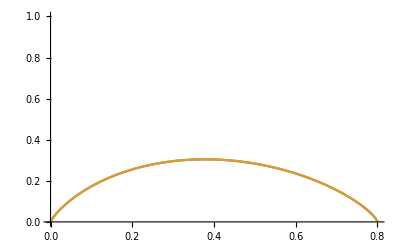

```mathematica
Plot[{
m(-Log[m/(1-0.2)])^((γ-1.)/γ),
m(-Log[(m+0.0001)/(1-0.2)])^((γ-1.)/γ)
},
{m,0,1},
PlotRange->{0,1}
]
```

```mathematica
Plot3D[
0.7m(-Log[m/p])^((γ-1.)/γ),
{m,0,1},
{p,0,1},
AxesLabel->Automatic

]
```

-Graphics3D-

### Решение

```mathematica
pde=eq/.fluxes/.rate/.rep/.bound;
pde=Activate[pde,D];

solPDE=Activate[pde∪ibcs]//N//FullSimplify;
solPDE//TableForm//TraditionalForm
```

n(0.,x)==0.1
p(0.,x)==0.001
n^(0,2)(t,x) (0.09 p(t,x)-0.1)+n^(1,0)(t,x)-0.09 n(t,x) p^(0,2)(t,x)+0.==NeumannValue[0.,x==-1.∨x==10.]
-4. If[2.<x<3.∧1. n(t,x)+1. p(t,x)≤0.9999,0.7 (-1. n(t,x)-1. p(t,x)+1.) (-1. log((-1. n(t,x)-1. p(t,x)+1.)/(1.-1. n(t,x))))^0.75,0.]-0.01 p^(0,2)(t,x)+1. p^(1,0)(t,x)==NeumannValue[0.,x==-1.∨x==10.]

```mathematica
Mon[Hold[solution=solve]]
```

27.5781

#### Check

```mathematica
{solutionCheck}=solveCheck
```

{NDSolve`StateData[<0.>]}

```mathematica
solutionCheck["FiniteElementData"]["Properties"][[2]]["Properties"]
```

FEMMethodData[Properties]

### Графики

```mathematica
(*
Шаг сетки для графика
*)
tstep = 0.1;
xstep = 0.01;

(*
Образование простых функций для вывода
*)
SOLn=
Table[
Table[
n[it,ix]/.solution,
{ix,xmin,xmax,xstep}
],
{it,0,tmax,tstep}
];
SOLn=ListInterpolation[SOLn,({{0, tmax}, {xmin, xmax}})];
SOLm=
Table[
Table[
1-n[it,ix]-p[it,ix]/.solution,
{ix,xmin,xmax,xstep}
],
{it,0,tmax,tstep}
];
SOLm=ListInterpolation[SOLm,({{0, tmax}, {xmin, xmax}})];
SOLp=
Table[
Table[
p[it,ix]/.solution,
{ix,xmin,xmax,xstep}
],
{it,0,tmax,tstep}
];
SOLp=ListInterpolation[SOLp,({{0, tmax}, {xmin, xmax}})];
(*
График
*)

Manipulate[
Plot[
{
SOLp[t,x],
SOLn[t,x],
SOLm[t,x]
},
{x,xmin,xmax},
PlotRange->{-0.1,1.1}
],
{t,0,tmax}
]
```